```mathematica
output1={
{0024,0.7986111253135713,0.0126959099588622,8.5390348341955296},{0034,0.3431276100898363,0.0078009764509949,2.1834075527609400},{0046,0.2516698683926846,0.0045156597315186,0.6552538386262441},{0066,0.1684904569262700,0.0023527299300810,0.3854031523938524},{0092,0.1327473753550956,0.0012913192714619,0.5758908126664437},{0130,0.0852591313242987,0.0006891707977750,0.3741785948343868},{0182,0.0487042542203073,0.0003711158430251,0.1460993950097382},{0258,0.0253329476624709,0.0001930308478815,0.0354456255930664},{0364,0.0129424620018765,0.0001001535310654,0.0070564096840720},{0514,0.0067258624763746,0.0000513975485388,0.0014401617243927},{0726,0.0046836744763674,0.0000261734849984,0.0003211383667576},{1026,0.0032965571231631,0.0000132418781351,0.0000756716294354},{1450,0.0023375870447719,0.0000066726644354,0.0000183749374862},{2050,0.0016633999511071,0.0000033504772312,0.0000045232811701},{2898,0.0011869253225778,0.0000016796636146,0.0000011234567872}
};
output2={
{0046,0.2353588470037469,0.0031647365624661,11.2063336206179756},{0066,0.2209674923186049,0.0015048876887396,1.0917037763805748},{0090,0.1645439665990929,0.0006113962632293,1.1890637931357402},{0130,0.0831374797900479,0.0001866860295998,0.1927015761969759},{0182,0.0346655673106633,0.0000578297408285,2.2950626793305116},{0258,0.0115291578947563,0.0000158536964312,0.2486789429422229},{0362,0.0034926340973769,0.0000042239397504,0.0913114840610714},{0514,0.0009517184418564,0.0000010484895112,0.0177228127965314},{0726,0.0002565118745257,0.0000002679234925,0.0038851330886818},{1026,0.0000673509975901,0.0000000685038613,0.0007200808697352},{1450,0.0000172432433820,0.0000000174910546,0.0001605691833770},{2050,0.0000043759095218,0.0000000043330430,0.0000378358147177},{2898,0.0000014058567366,0.0000000012099661,0.0000091874899759}
};
nShow=1;
nFit=-5;
eD1=output1⟦nShow;;-1,{1,2}⟧;
eD2=output2⟦nShow;;-1,{1,2}⟧;
eN1=output1⟦nShow;;-1,{1,3}⟧;
eN2=output2⟦nShow;;-1,{1,3}⟧;
eK=output2⟦nShow;;-1,{1,-1}⟧;
fD1 = Normal@LinearModelFit[Log10@eD1⟦nFit;;-1⟧,{x},x]
fD2 = Normal@LinearModelFit[Log10@eD2⟦nFit;;-1⟧,{x},x]
fN1 = Normal@LinearModelFit[Log10@eN1⟦nFit;;-1⟧,{x},x]
fN2 = Normal@LinearModelFit[Log10@eN2⟦nFit;;-1⟧,{x},x]
fK = Normal@LinearModelFit[Log10@eK⟦nFit;;-1⟧,{x},x]
```

0.503541-0.990989 x

7.2629-3.79897 x

1.09588-1.98421 x

4.63374-3.9186 x

9.97865-4.34607 x

```mathematica
tk=AbsoluteThickness[1];
cm=72/2.54;
g1={t/(π/2)1.5,0};
g2=2(1+1/4 Cos[8t - π]){Sin[t],Cos[t]};
ysize=5cm;
```

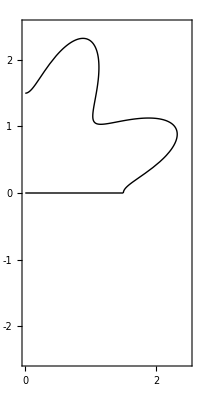

```mathematica
ticks[min_,max_]:=Table[If[FractionalPart[i]==0.,{i,Floor@i,{.0,-0.04},Directive[Black,tk]},{i,"",{.0,-0.02},Directive[Black,tk]}],{i,Floor[min],Ceiling[max],0.2}]
o1=ParametricPlot[{g1,g2},{t,0,π/2},PlotStyle->Directive[Black,tk]
,PlotRange->{{0,2.5},2.5{-1,1}},Axes->False,Frame->True,AspectRatio->Automatic,

FrameTicks->{{ticks,None},{ticks,None}},ImageSize->{Automatic,ysize} 
]
```

```mathematica
FractionalPart[2.8/0.2]
```

0.

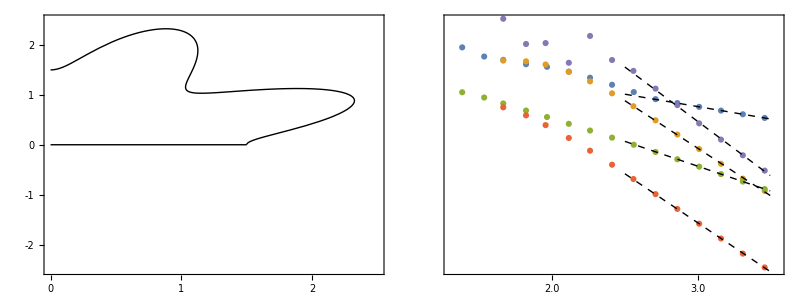

```mathematica
majorTicLength=0.015;
minorTicLength=majorTicLength/2;
tickx[min_,max_]:=Table[If[Abs@FractionalPart[i*2]<0.0001,{i,NumberForm[i,{2,1}],{.0,-majorTicLength},Directive[Black,tk]},{i,"",{.0,-minorTicLength},Directive[Black,tk]}],{i,Floor[min],Ceiling[max],0.1}]
ticky[min_,max_]:=Table[If[FractionalPart[i]==0.,{i,i,{.0,-majorTicLength},Directive[Black,tk]},{i,"",{.0,-minorTicLength},Directive[Black,tk]}],{i,Floor[min],Ceiling[max],0.2}]
o2=Show[
ListPlot[Log10@{eD1,eD2,eN1,eN2,eK}],
Plot[{fD1,fD2,fN1,fN2,fK},{x,2.5,3.5},PlotStyle->Directive[Black,Dashed,tk]],
FrameTicks->{{None,ticky},{tickx,None}},AspectRatio->1/1.61803398875
,PlotRange->{{1.3,3.55},{-9,1}},
Frame->True,ImageSize->{Automatic,ysize} ,Axes->False,
BaseStyle->{FontFamily->"Times New Roman"}

];
Grid[{{o1,o2}}]
```

```mathematica
Style["a",FontFamily->]
```

```mathematica
2.8
```

2.8

0.024

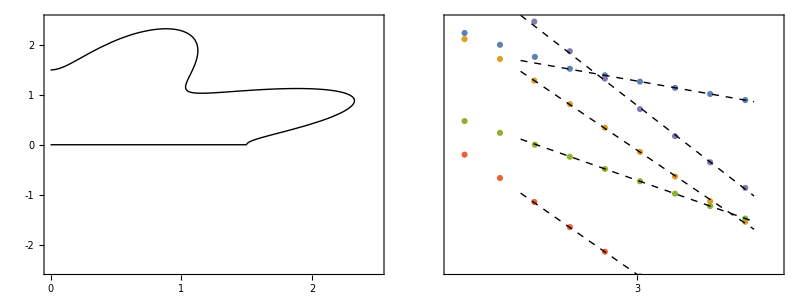

```mathematica
6/(5/0.02)
```

```mathematica
x[θ_]=2(1+1/4 Cos[8 θ - π])Sin[θ];
y[θ_]=2(1+1/4 Cos[8 θ - π])Cos[θ];
(x'[θ] y''[θ]-y'[θ] x''[θ])/((x'[θ]^2+y'[θ]^2)^(3/2))+1/x[θ] y'[θ]/(√(x'[θ]^2+y'[θ]^2))//FullSimplify
ToString@CForm[%]
ToLowerCase@%
StringReplace[%,{"θ"->"theta","power"->"pow","cot"->"1./tan"}]
```

-(8 √2 (33 Cos[8 θ]^3+Cos[8 θ] (560-32 Cot[θ] Sin[8 θ])+4 Cos[8 θ]^2 (-67+Cot[θ] Sin[8 θ])+64 (-4+3 Cos[16 θ]+Cot[θ] (Sin[8 θ]+4 Sin[8 θ]^3))+48 Sin[8 θ] Sin[16 θ]))/((-4+Cos[8 θ]) (97-16 Cos[8 θ]-63 Cos[16 θ])^(3/2))

(-8*Sqrt(2)*(33*Power(Cos(8*θ),3) + Cos(8*θ)*(560 - 32*Cot(θ)*Sin(8*θ)) + 4*Power(Cos(8*θ),2)*(-67 + Cot(θ)*Sin(8*θ)) + 64*(-4 + 3*Cos(16*θ) + Cot(θ)*(Sin(8*θ) + 4*Power(Sin(8*θ),3))) + 48*Sin(8*θ)*Sin(16*θ)))/((-4 + Cos(8*θ))*Power(97 - 16*Cos(8*θ) - 63*Cos(16*θ),1.5))

(-8*sqrt(2)*(33*power(cos(8*θ),3) + cos(8*θ)*(560 - 32*cot(θ)*sin(8*θ)) + 4*power(cos(8*θ),2)*(-67 + cot(θ)*sin(8*θ)) + 64*(-4 + 3*cos(16*θ) + cot(θ)*(sin(8*θ) + 4*power(sin(8*θ),3))) + 48*sin(8*θ)*sin(16*θ)))/((-4 + cos(8*θ))*power(97 - 16*cos(8*θ) - 63*cos(16*θ),1.5))

(-8*sqrt(2)*(33*pow(cos(8*theta),3) + cos(8*theta)*(560 - 32*1./tan(theta)*sin(8*theta)) + 4*pow(cos(8*theta),2)*(-67 + 1./tan(theta)*sin(8*theta)) + 64*(-4 + 3*cos(16*theta) + 1./tan(theta)*(sin(8*theta) + 4*pow(sin(8*theta),3))) + 48*sin(8*theta)*sin(16*theta)))/((-4 + cos(8*theta))*pow(97 - 16*cos(8*theta) - 63*cos(16*theta),1.5))

```mathematica
-(8 √2 (33 Cos[8 θ]^3+Cos[8 θ] (560-32 Cot[θ] Sin[8 θ])+4 Cos[8 θ]^2 (-67+Cot[θ] Sin[8 θ])+64 (-4+3 Cos[16 θ]+Cot[θ] (Sin[8 θ]+4 Sin[8 θ]^3))+48 Sin[8 θ] Sin[16 θ]))/((-4+Cos[8 θ]) (97-16 Cos[8 θ]-63 Cos[16 θ])^(3/2))
Limit[%,θ->0]
```

-(8 √2 (33 Cos[8 θ]^3+Cos[8 θ] (560-32 Cot[θ] Sin[8 θ])+4 Cos[8 θ]^2 (-67+Cot[θ] Sin[8 θ])+64 (-4+3 Cos[16 θ]+Cot[θ] (Sin[8 θ]+4 Sin[8 θ]^3))+48 Sin[8 θ] Sin[16 θ]))/((-4+Cos[8 θ]) (97-16 Cos[8 θ]-63 Cos[16 θ])^(3/2))

244/9

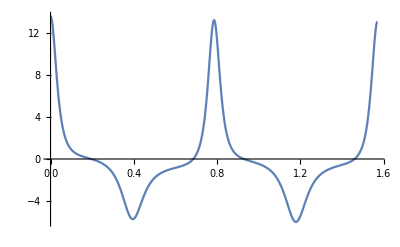

```mathematica
Plot[(x'[θ] y''[θ]-y'[θ] x''[θ])/((x'[θ]^2+y'[θ]^2)^(3/2))+1/2 y'[θ]/(√(x'[θ]^2+y'[θ]^2)),{θ,0,π/2},PlotRange->All]
```